```mathematica
RelationGraph[!CoprimeQ[#1,#2]&,{2,3,4,5,6}]
```

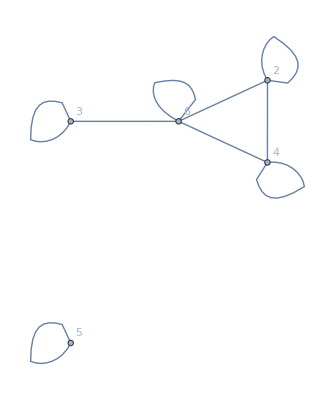

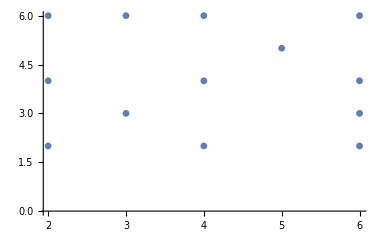

```mathematica
ListPlot[Select[Tuples[Range[6],2],!CoprimeQ[#[[1]],#[[2]]]&]]
```

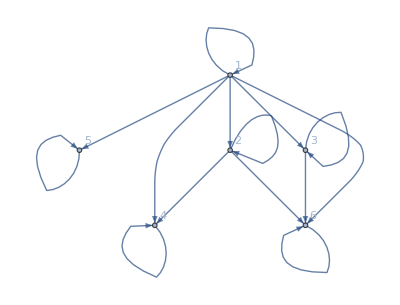

```mathematica
RelationGraph[Divisible[#2,#1]&,{1,2,3,4,5,6}]
```

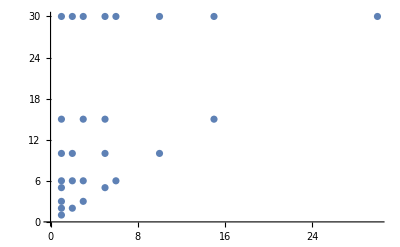

```mathematica
ListPlot[Select[Tuples[Divisors[30],2],Divisible[#[[2]],#[[1]]]&]]
```

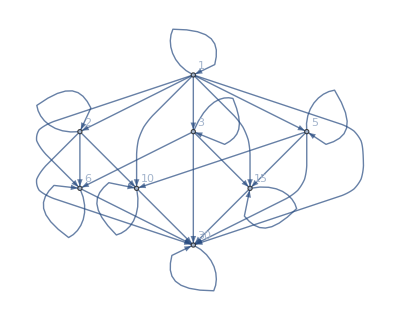

```mathematica
RelationGraph[Divisible[#2,#1]&,Divisors[30]]
```

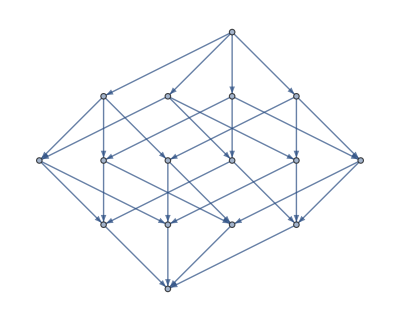

```mathematica
RelationGraph[PrimeQ[#2/#1]&,Divisors[30 7]]
```